```mathematica
import[n_]:=Import["https://www.jeremieturcotte.com/research/min4cops/data/maxdeg3/results/3copwingraphs/n"<>ToString[n]<>"d2D3_3cops.g6","Graph6"]
```

```mathematica
list=Flatten[Table[{import[n]},{n,{10,12,14,15,16,17,18,19,20}}]]; (* The list of subcubic 3-cop win graphs between 10 and 20 vertices (there are none on 11, 13 vertices)*)
```

```mathematica
list//Length
```

30705

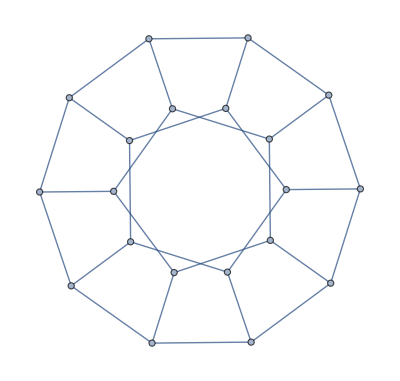

```mathematica
planarlist=Select[list,PlanarGraphQ] (* We select the graphs which are also planar. *)
```

```mathematica
IsomorphicGraphQ[planarlist[[1]],GraphData["DodecahedralGraph"]] (* The only such graph is the dodecahedral graph. *)
```

True